### Lab 5, PHY304, Kristen

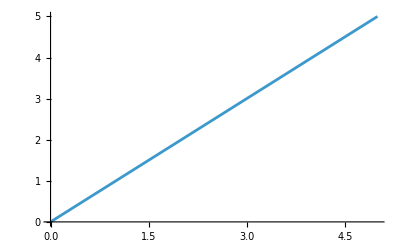

```mathematica
Plot[x,{x,0,5}]
```

```mathematica
D[α Log[a t]Cos[ω t] Sin[ω t],t]
```

α ω Cos[t ω]^2 Log[a t]+(α Cos[t ω] Sin[t ω])/t-α ω Log[a t] Sin[t ω]^2

```mathematica
D[α Log[a t]Cos[ω t] Sin[ω t],{t,2}]
```

-α ω^2 Cos[t ω] Log[a t] Sin[t ω]-2 α ω Sin[t ω] (ω Cos[t ω] Log[a t]+Sin[t ω]/t)+α Cos[t ω] ((2 ω Cos[t ω])/t-Sin[t ω]/t^2-ω^2 Log[a t] Sin[t ω])

```mathematica
D[f[x] g[x] h[x],{x}]
```

g[x] h[x] f'[x]+f[x] h[x] g'[x]+f[x] g[x] h'[x]

```mathematica
l=10
g=9.8
ω=Sqrt[g/l]
s=NDSolve[{y''[ϕ]==-ω^2 Sin[y[ϕ]],y[0]==π/6, y'[0]==0},y,{ϕ,0,30}]
```

10

9.8

0.989949

{{y→InterpolatingFunction[…]}}

```mathematica
NDSolve[{y''[ϕ]==-1/10 Sin[ϕ] TerminatedEvaluation["RecursionLimit"]+y[ϕ],y[0]==π/6,y'[0]==0},y,{ϕ,0,30}]
```

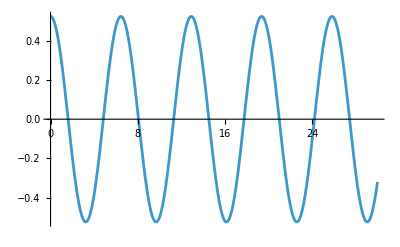

```mathematica
Plot[Evaluate[y[ϕ]/. s],{ϕ,0,30},PlotRange->All]
```

```mathematica
Graphics3D[{Cylinder[{{0,0,0},{0,0,1}},5],Cylinder[{{0,0,0},{0,0,10}},.5]}]
```

-Graphics3D-

NDSolve::argm: NDSolve called with 2 arguments; 3 or more arguments are expected.